## For a general optimal control problem

### Need to minimize functional such as J = (∫_0)^T{L(x(t),u(t)) - λ(t) (dx/dt - f(x(t),u(t)) } dt where we assume that the Langrangian L and the cost function f do not depend explicitly on time nor on derivatives of x and u. Also, the final time T is fixed.

### The solution to this optimization, with these assumption, yields these 4 conditions: 1) H = L + λ f = constant, where H is the Hamiltonian, 2) dλ/dt=-((∂L)/(∂x)+λ (∂f)/(∂x)), 3) (∂L)/(∂u)+λ (∂f)/(∂u)=0, 4) dx/dt=f(x,u).

## Equation derivation: no direct g boundary set by soil moisture

In the case of photosynthesis, the photosynthetic rate A(x(t),g(t)) needs to be maximized (replacing L(x(t),g(t)). It depends on the stomatal conductance g(t) and the soil moisture x(t). However, during drydown the cost function is the reduction of soil moisture with time dx/dt=f(g,x). Based on ecohydrological approaches, f = -(L + E)/(n Z_r) where L is the soil leakage term, E is the evapotranspiration term, n is the soil porosity, and Z_r is the rooting depth.
If g << g_a where g_a is the boundary-layer conductance, then E(t) = ν a g(t) D. The value ν is there to convert to the appropriate units, a = 1.6 is the ratio of water vapor to CO2 diffusivity, and D is the vapor pressure deficit of water. The leakage L is written as a power law of soil moisture L(t) = γ (x(t))^c
A = (g(t)c_a k)/(g(t) + k), where c_a is the atmospheric CO2 concentration and k is the carboxylation efficiency.

With these terms defined we can write the following conditions:
1) (g(t) c_a k)/(g(t) + k)-λ(t) (γ (x(t))^c+ν a g(t) D)/(n Z_r) = constant = H,
2) (dλ(t))/dt= - (0 -(λ(t) γ c (x(t))^(c-1))/(n Z_r))=(λ(t) γ c (x(t))^(c-1))/(n Z_r),
3) (c_a k^2)/[g(t)+k]^2-(ν a D λ(t))/(n Z_r)=0,
4) (dx(t))/dt=-(γ (x(t))^c+ν a g(t) D)/(n Z_r).

```mathematica
Column[{
"Table of constants",
Grid[{
{"γ","α","β","ν"},
{Column[{"moisture power-law","L(t) = γ x(t)"},Center],"(ν a)/(n SubscriptBox[Z, r])","γ","(LAI SubscriptBox[M, w])/ρ_w"}
},Dividers->All]
},Center]
```

Table of constants
γ | α | β | ν
moisture power-law
L(t) = γ x(t) | (ν a)/(n SubscriptBox[Z, r]) | γ | (LAI SubscriptBox[M, w])/ρ_w

## Leakage losses independent of soil moisture (c=0)

```mathematica
Grid[{
{"x(t)","β=γ/(n SubscriptBox[Z, r])","c","λ(t)"},
{0, "≥0", 0,"λ_0"}
},Dividers->All]
```

x(t) | β=γ/(n SubscriptBox[Z, r]) | c | λ(t)
0 | ≥0 | 0 | λ_0

```mathematica
optg=Last[DSolve[(ca (k)^2)/(g[t]+k)^2-(ν a VPD λ)/(n Zr)==0,g[t] ,t ]]//Simplify
```

{g[t]→k (-1+(√ca √n √Zr)/(√a √VPD √λ √ν))}

```mathematica
optx=Collect[First[DSolve[{x'[t]==-(γ+ν a g[t]VPD)/(n Zr),x[0]==x0}/.optg,x[t],t]],t]
```

{x[t]→x0+(t (-γ √λ-√a √ca k √n √VPD √Zr √ν+a k VPD √λ ν))/(n Zr √λ)}

```mathematica
optLam=First[Solve[((x[t]/.optx)/.t->T)==0,λ]]
```

{λ→(a ca k^2 n T^2 VPD Zr ν)/(n x0 Zr-T γ+a k T VPD ν)^2}

An asymptote could exists as can be seen from the denominator of λ.

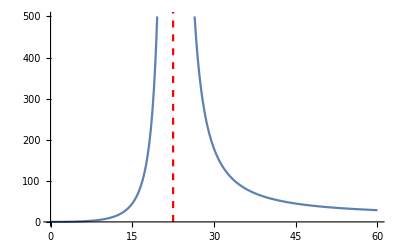

```mathematica
constants={T->Quantity[t,"Days"],γ->Quantity[0.01, ("Meters")/("Days")],VPD->Quantity[0.015, ("Moles")/("Moles")],k->Quantity[0.05, ("Moles")/(("Meters")^2 "Seconds")],x0->0.8,Zr->Quantity[0.3, "Meters"],ca->Quantity[350, ("Micromoles")/("Moles")],a->1.6,n->Quantity[0.5, ("Meters")^3/("Meters")^3],ν->(Quantity[5, ("Meters")^2/("Meters")^2]*Quantity[0.018, ("Kilograms")/("Moles")]*Quantity[12, ("Hours")/("Days")])/Quantity[1000, ("Kilograms")/("Meters")^3]};
lamSol=λ/.optLam/.constants;
asymptoteAbscissa=QuantityMagnitude[((-x0 n Zr)/(ν a k VPD - γ))/.constants];
Show[
Plot[Evaluate[UnitConvert[lamSol*(ν/(n Zr)/.constants),"Millimoles"/"Moles"]/.t->T],{T,0,60},PlotRange->{0,500}],
ListLinePlot[{{asymptoteAbscissa,0},{asymptoteAbscissa,10000}},PlotStyle->{Red,Dashed}]
]
```

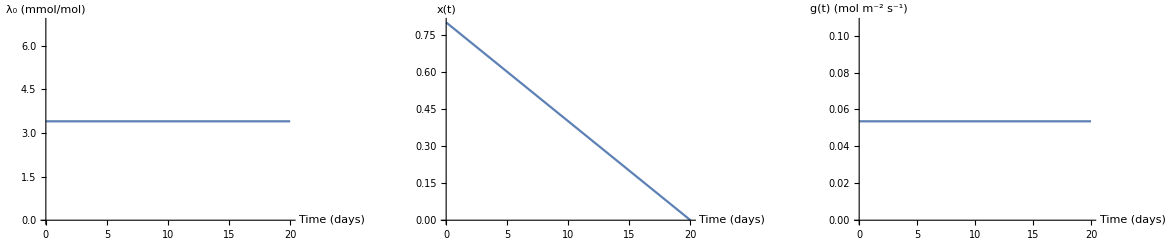

```mathematica
Clear[lamSol]
constants={T->Quantity[20, "Days"],γ->Quantity[0.001, ("Meters")/("Days")],VPD->Quantity[0.015, ("Moles")/("Moles")],k->Quantity[0.05, ("Moles")/(("Meters")^2 "Seconds")],x0->0.8,Zr->Quantity[0.3, "Meters"],ca->Quantity[350, ("Micromoles")/("Moles")],a->1.6,n->Quantity[0.5, ("Meters")^3/("Meters")^3],ν->(Quantity[5, ("Meters")^2/("Meters")^2]*Quantity[0.018, ("Kilograms")/("Moles")]*Quantity[12, ("Hours")/("Days")])/Quantity[1000, ("Kilograms")/("Meters")^3]};
lamSol[t_]:=λ/.optLam/.constants;
xSol[t_]:=x[t]/.optx/.constants/.λ->lamSol[t];
gSol[t_]:=g[t]/.optg/.constants/.λ->lamSol[t];
lambdaPlot=Plot[UnitConvert[lamSol[t]*(ν/(n Zr)/.constants),"Millimoles"/"Moles"],{t,0,20},
AxesLabel->{"Time (days)","λ_0 (mmol/mol)"},ImageSize->Medium];
xPlot=Plot[Evaluate[xSol[t]/.t->Quantity[t,"Days"]],{t,0,20},
AxesLabel->{"Time (days)","x(t)"}];
gPlot=Plot[Evaluate[gSol[t]/.t->Quantity[t,"Days"]],{t,0,20},
AxesLabel->{"Time (days)","g(t) ("<>"mol m^-2 s^-1"<>")"}];
GraphicsRow[{lambdaPlot,xPlot,gPlot}]
```

```mathematica
ClearAll[lamSol,λ,x]
```

## What if leakage losses depend linearly on soil moisture? (c=1)

```mathematica
optLam=First[DSolve[{λ'[t]== (λ[t] β)/1,λ[0]==λ0},λ[t],t]]//Simplify;
optg=Last[DSolve[(ca (k)^2)/(g[t]+k)^2-(α VPD λ[t])/1==0,g[t] ,t ]]/.optLam//Simplify;
optx=
First[
DSolve[
Evaluate[{x'[t]==-(β x[t]+α g[t]VPD)/1,x[0]==x0}/.Flatten[{optg,optLam}]]
,x[t],t]
]//Expand;
Column[{
optLam//TraditionalForm,
optg//TraditionalForm,
optx//TraditionalForm
}]
```

{λ(t)→λ0 ⅇ^(β t)}
{g(t)→k ((√ca)/(√α √VPD √(λ0 ⅇ^(β t)))-1)}
{x(t)→-(2 √α √ca k √VPD ⅇ^(β (-t)) √(λ0 ⅇ^(β t)))/(β λ0)+(2 √α √ca k √VPD ⅇ^(β (-t)))/(β √λ0)-(α k VPD ⅇ^(β (-t)))/β+(α k VPD)/β+x0 ⅇ^(β (-t))}

```mathematica
lamIni=Collect[FullSimplify[First[Solve[((x[t]/.optx)/.t->T)==0,λ0]]],{ca,k}]
```

{λ0→(4 ca (1+ⅇ^(T β)) k^2 VPD α ((-1+ⅇ^(T β)) k VPD α+x0 β)^2-8 √(ca^2 ⅇ^(T β) k^4 VPD^2 α^2 ((-1+ⅇ^(T β)) k VPD α+x0 β)^4))/(((-1+ⅇ^(T β)) k VPD α+x0 β)^4)}

```mathematica
Reduce[Denominator[Evaluate[λ0/.lamIni]]==0,T]
```

(k==0&&x0==0)||(k≠0&&((VPD==0&&x0==0)||(x0≠0&&VPD==0&&β==0)))||(k VPD≠0&&((x0==0&&α==0)||(x0≠0&&α==0&&β==0)))||(k VPD α≠0&&((k VPD α≠0&&x0==0&&β==0)||β==0))||(x0≠0&&k==0&&β==0)||(C[1]∈ℤ&&k VPD α≠0&&k VPD α-x0 β≠0&&β≠0&&T==(2 ⅈ π C[1]+Log[(k VPD α-x0 β)/(k VPD α)])/β)

So compared to when c=0, this case has no singularity

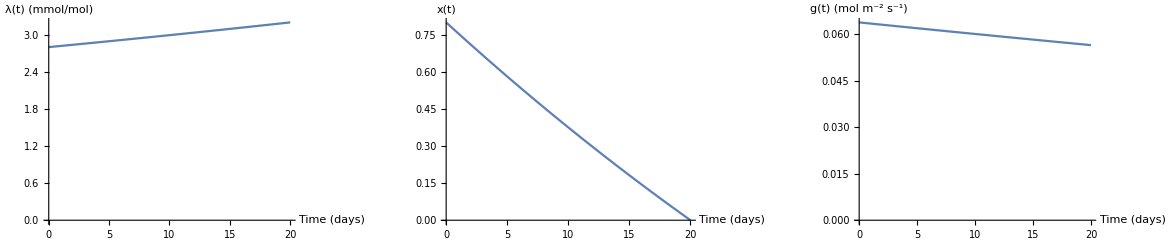

```mathematica
constants={T->Quantity[20, "Days"],γ->Quantity[0.001, ("Meters")/("Days")],VPD->Quantity[0.015, ("Moles")/("Moles")],k->Quantity[0.05, ("Moles")/(("Meters")^2 "Seconds")],x0->0.8,Zr->Quantity[0.3, "Meters"],ca->Quantity[350, ("Micromoles")/("Moles")],a->1.6,n->Quantity[0.5, ("Meters")^3/("Meters")^3],ν->(Quantity[5, ("Meters")^2/("Meters")^2]*Quantity[0.018, ("Kilograms")/("Moles")]*Quantity[12, ("Hours")/("Days")])/Quantity[1000, ("Kilograms")/("Meters")^3]};
lamSol[t_]:=λ[t]/.optLam/.lamIni/.{β->γ/(n Zr),α->(ν a)/(n Zr)}/.constants;
xSol[t_]:=x[t]/.optx/.lamIni/.{β->γ/(n Zr),α->(ν a)/(n Zr)}/.constants/.λ[t]->lamSol;
gSol[t_]:=g[t]/.optg/.lamIni/.{β->γ/(n Zr),α->(ν a)/(n Zr)}/.constants/.λ[t]->lamSol;
lambdaPlot=Plot[Evaluate[UnitConvert[(lamSol[t]*(ν/(n Zr)/.constants))/.t->Quantity[t,"Days"],"Millimoles"/"Moles"]],{t,0,20},
AxesLabel->{"Time (days)","λ(t) (mmol/mol)"},ImageSize->Medium,PlotRange->{0,Automatic}];
xPlot=Plot[Evaluate[xSol[t]/.t->Quantity[t,"Days"]],{t,0,20},
AxesLabel->{"Time (days)","x(t)"},PlotRange->{0,Automatic}];
gPlot=Plot[Evaluate[gSol[t]/.t->Quantity[t,"Days"]],{t,0,20},
AxesLabel->{"Time (days)","g(t) ("<>"mol m^-2 s^-1"<>")"},PlotRange->{0,Automatic}];
GraphicsRow[{lambdaPlot,xPlot,gPlot}]
```

```mathematica
lamSol[t]/.t->LinguisticAssistant
```

9.36688×10^6 µmol/m^2

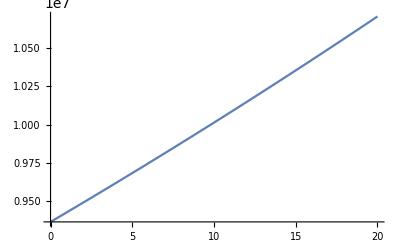

```mathematica
Plot[Evaluate[lamSol[t]/.t->Quantity[t,"Days"]],{t,0,20}]
```

```mathematica
Clear[optLam,optg,optx,lamIni,lamSol,xSol,gSol]
```

## g is bounded by soil moisture

This condition is formulated as g(t)≤g_b(t)  where g_b(t) = k_SR/(ν a VPD)x(t). This formula is a direct consequence of assuming the following E_SR=k_SR x(t) where SR refers to soil-root. So the transpiration level is limited by water supply from the soil to the roots. See Porporato’s papers and books about how this relation should in fact be non-linear.
What would the soil moisture equation look like in the soil moisture limitation case?

```mathematica
optxLim=
First[
DSolve[
Evaluate[{x'[t]==-(β x[t]+α kSR/(ν a VPD) x[t] VPD)/1,x[0]==x0}]
,x[t],t]
]//Expand;
optxLim//TraditionalForm
```

{x(t)→x0 ⅇ^(α (-kSR) t VPD-β t)}

```mathematica
optg=Last[DSolve[(ca (k)^2)/(g[t]+k)^2-(α VPD λ[t])/1==0,g[t] ,t ]]//Simplify
```

{g[t]→k (-1+(√ca)/(√VPD √α √λ[t]))}

```mathematica
Solve[(g[t]/.optg)==kSR/(ν a VPD) x[t],λ[t]]
```

{{λ[t]→(a^2 ca k^2 VPD ν^2)/(α (a k VPD ν+kSR x[t])^2)}}

Let’s first solve the system completely numerically:

```mathematica
Clear[λ]
```

```mathematica
Manipulate[
constants={T->20,γ->0.001,VPD->0.015,k->0.05*24*3600,x0->0.8,Zr->0.3,ca->350*^-6,a->1.6,n->0.5,ν->(5*0.018*0.5)/1000,kSR->kSRvar};
sols=NDSolve[{λ'[t]== (λ[t] β)/1,x'[t]==-(β x[t]+α g[t]VPD)/1,x[0]==x0,x[T]==0,WhenEvent[k (-1+(√ca)/(√VPD √α √λ[t]))-kSR/(ν a VPD) x[t]≥0,"StopIntegration"]}/.
optg/.{β->γ/(n Zr),α->(ν a)/(n Zr)}/.constants,
{x,λ},{t,0,20}];
tStar=(x/.sols)[[1,1,1,2]];
sols2=First[DSolve[
Evaluate[{x'[t]==-(β x[t]+α kSR/(ν a VPD) x[t] VPD)/1,x[tStar]==First[x[tStar]/.sols]}/.{β->γ/(n Zr),α->(ν a)/(n Zr)}/.constants]
,x[t],t]];
xSol[t]=Piecewise[{{First[x[t]/.sols], t<tStar}, {x[t]/.sols2, t≥tStar}}];
lamSol[t]=Piecewise[{{λ[t]/.sols, t<tStar}, {(a^2 ca k^2 VPD ν^2)/(α (a k VPD ν+kSR x[t])^2)/.{β->γ/(n Zr),α->(ν a)/(n Zr)}/.constants/.sols, t≥tStar}}];
gSol[t]=Piecewise[{{g[t]/.optg/.sols/.{β->γ/(n Zr),α->(ν a)/(n Zr)}/.constants//First, t<tStar}, {kSR/(ν a VPD) x[t]/.{β->γ/(n Zr),α->(ν a)/(n Zr)}/.constants/.sols2, t≥tStar}}];
GraphicsRow[{
Plot[xSol[t],{t,0,20},PlotRange->{0,Automatic},AxesLabel->{"Time (Days)","x(t)"},
Epilog->{PointSize[Medium],Red,Point[{tStar,xSol[t]/.t->tStar}]},ImageSize->Medium],
Plot[lamSol[t]*(ν/(n Zr)/.constants)*10^3,{t,0,20},PlotRange->{0,Automatic},AxesLabel->{"Time (Days)","λ(t) (mmol mol^-1)"},
Epilog->{PointSize[Medium],Red,Point[{tStar,First[lamSol[t]*(ν/(n Zr)/.constants)*10^3/.t->tStar]}]}],
Plot[gSol[t]/(24*3600),{t,0,20},PlotRange->{0,Automatic},AxesLabel->{"Time (Days)","g(t) (mol m^-2 s^-1)"},
Epilog->{PointSize[Medium],Red,Point[{tStar,gSol[t]/(24*3600)/.t->tStar}]}]
}]
,{kSRvar,0.01,0.1,Appearance->"Labeled"}]
```

```mathematica
?Point*
```

System`PointBox

Attributes[PointBox]={HoldAll,Protected,ReadProtected}